```mathematica
Get[NotebookDirectory[]<>#]&/@
{"combine_packages.wls",
"load_hill_data.wl"
};
```

```mathematica
figureNameDaily="daily_dynamics";
figureDirectoryDaily=figureNameDaily;
```

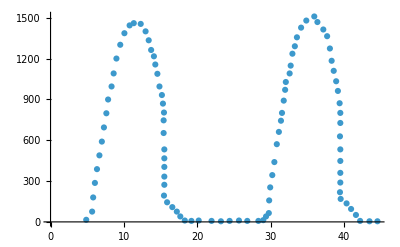

```mathematica
ListPlot[SortBy[dataHill["Light"],#[[1]]&]]
```

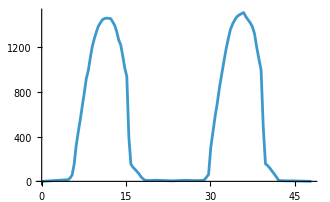

```mathematica
interpolHill["Light"]=Interpolation[Join[{{0,0}},({Mean[#[[All,1]]],Max[0,Mean[#[[All,2]]]]}&)/@GatherBy[dataHill["Light"],First],{{48,0}}]
,InterpolationOrder->1];
Plot[interpolHill["Light"][t],{t,0,48},PlotPoints->3,AxesOrigin->{0,0}]
```

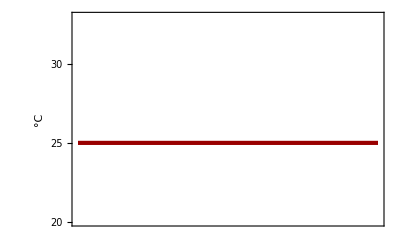
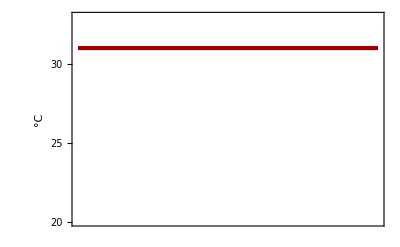

```mathematica
colorsHill=#[[1]]->(#[[2]]/.colorsBase)&/@{"FvFm"->"FvFm","YII"->"P","YNPQ"->"N","YNO"->"U","w"->"w"};
minRangesHill={"w"->20,_->Automatic};
maxRangesHill={"FvFm"->0.7,"YII"->0.25,"YNPQ"->0.7,"YNO"->0.75,"L"->1600,"w"->33};
temperaturesHill={25,31};
ImagePaddingNoUnits={{20,0},{30,0}};
ImagePaddingLeftUnit1=ImagePaddingNoUnits+{{8,0},{0,0}};
ImagePaddingLeftUnit2=ImagePaddingNoUnits+{{20,0},{0,0}};
experimentPlotHillTemperature=Table[Plot[temperature,{t,26,46},AxesOrigin->Automatic,FrameTicks->{autoTicks,{{#[[1]]/3600,#[[2]]}&/@dayTicks,None}},FrameLabel->{{w/.units,None},{None,None}},Evaluate@imageSizePadding[ImagePaddingLeftUnit1],PlotRange->{{26,46},{(-0.05("w"/.minRangesHill))+1.05("w"/.minRangesHill),"w"/.maxRangesHill}},PlotStyle->{thickness,("w"/.colorsHill)/.colors},Evaluate@style],{temperature,temperaturesHill}]
```

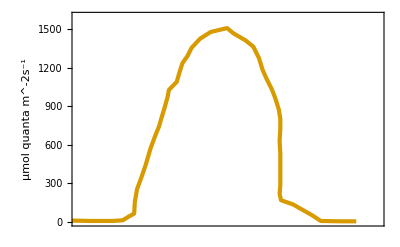

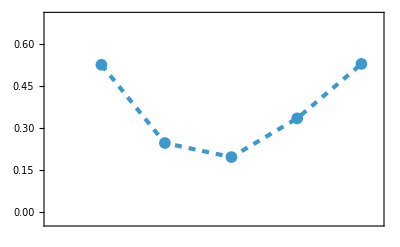
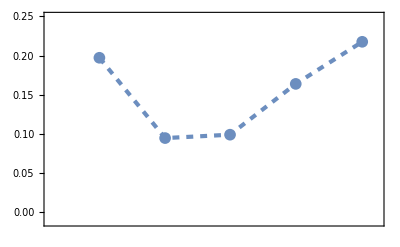
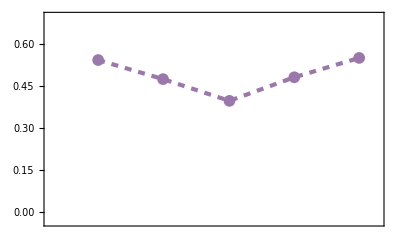
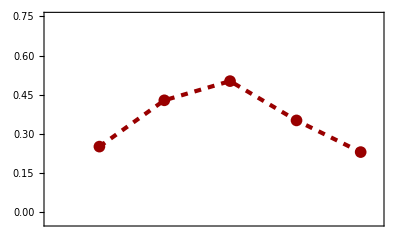
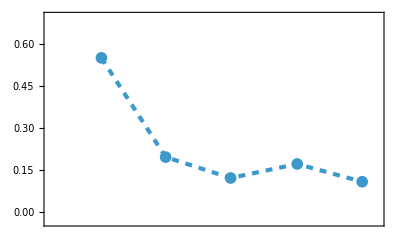
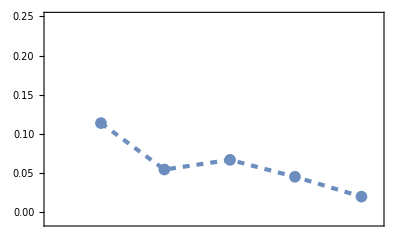
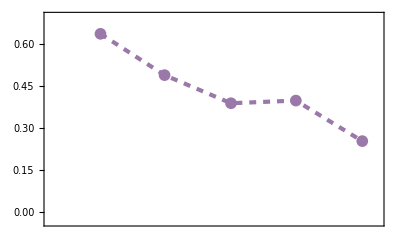

```mathematica
dataPlotHillLight=ListPlot[dataHill["Light"],Joined->True,FrameLabel->{{L/.units,None},{None,None}},Evaluate@imageSizePadding[ImagePaddingLeftUnit2],PlotStyle->{thickness,("L"/.colorsBase)},PlotMarkers->None,PlotRange->{{26,46},{(-0.05"L"/.maxRangesHill )+1.05"L"/.minRangesHill,1"L"/.maxRangesHill}},AxesOrigin->Automatic,FrameTicks->{autoTicks,{{#[[1]]/3600,#[[2]]}&/@dayTicks,None}},style]
dataPlotsHill=Table[ListPlot[Select[dataHill[x,y],#[[1]]>24&],Joined->True,Evaluate@imageSizePadding[ImagePaddingLeftUnit1],PlotStyle->{thickness,(x/.colorsHill)/.colors,Dashed},PlotMarkers->plotMarkers,PlotRange->{{26,46},{-0.05,1}x/.maxRangesHill},AxesOrigin->Automatic,FrameTicks->{autoTicks,{{#[[1]]/3600,#[[2]]}&/@dayTicks,None}},style],{y,{"Control","Bleaching"}},{x,{"FvFm","YII","YNPQ","YNO"}}]
```

```mathematica
dailyLmax=1800;
dailyPars=Join[
{
L->(Lmax Max[0.001,Sin[(2 π)/(3600 24) t-π/2],0]/.Lmax->dailyLmax),
tmin->0,
tmax->3600 24
},
pars[4]];
```

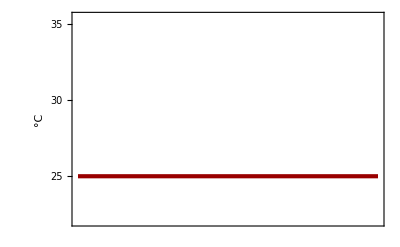
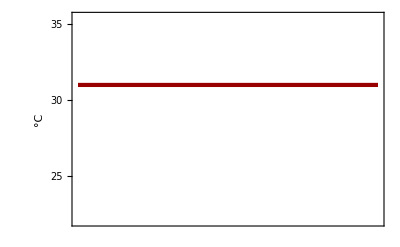

```mathematica
(*temperatureEpilog[i_]:={Epilog->Inset[Piecewise[{{Row[{Style["Moderate temperature ",12],Rasterize[Magnify[widgetModerate,.3]]}], i==1}, {Row[{Style["Heat stress  ",12],Rasterize[Magnify[widgetHeat,.7]]}], i==2}}],Scaled@{.6,.9}]};*)
minRangesHillSimulations={w->22,_->0};
maxRangesHillSimulations={FvFm->0.7,YP->.8,YN->0.7,YU->1,w->35.5};
dailyTemps={25,31}(*{28,33}*);
simulationPlotsHillTemperature=Table[plotSimulation[dailyTemps[[i]],Join[{w->28},dailyPars],{2 3600,22 3600},{Evaluate@imageSizePadding[ImagePaddingLeftUnit1],FrameTicks->{autoTicks,{dayTicks,None}},FrameLabel->{{w/.units,None},{None,None}},PlotRange->{{2 3600,22 3600},{(-0.05(w/.minRangesHillSimulations))+1.05(w/.minRangesHillSimulations),w/.maxRangesHillSimulations}},PlotStyle->{{thickness,w/.colors}}(*,temperatureEpilog[i]*)}],{i,2}]
```

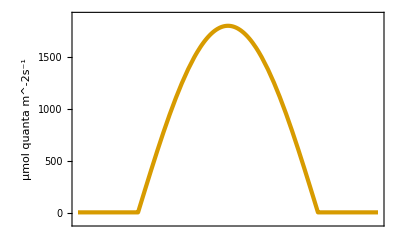

```mathematica
simulationPlotsHillLight=plotSimulation[L,Join[{w->28},dailyPars],{2 3600,22 3600},{FrameLabel->{{L/.units,None},{None,None}},PlotStyle->{{thickness,"L"/.colorsBase}},Evaluate@imageSizePadding[ImagePaddingLeftUnit2],FrameTicks->{autoTicks,{dayTicks,None}},PlotRange->{{2 3600,22 3600},{-0.05,1.05}dailyLmax/.maxRangesHillSimulations}}]
```

```mathematica
(*simulationPlotsHillTemperature=Table[Table[showDailySimu[x,Join[{w->temp},dailyPars],{2 3600,22 3600},{PlotStyle->{{thickness,x/.colors}},FrameLabel->{{x/.units,None},{None,None}},FrameTicks->{autoTicks,{dayTicks,None}},Evaluate@imageSizePadding[ImagePaddingLeftUnit1],PlotRange->{{2 3600,22 3600},{(-0.05(x/.maxRangesHillSimulations))+1.05(x/.minRangesHillSimulations),x/.maxRangesHillSimulations}}}],{x,{FvFm,YP,YN,YU}}],{temp,dailyTemps}]*)
```

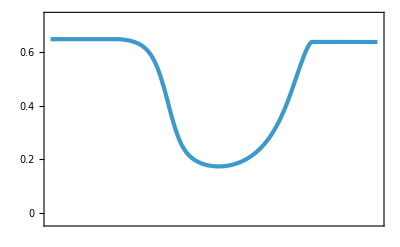
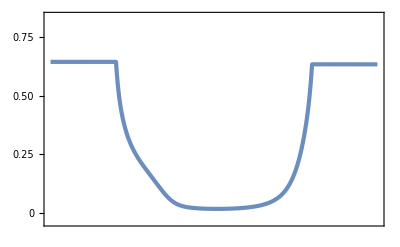
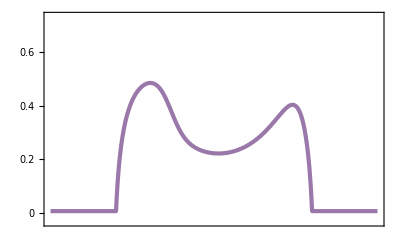
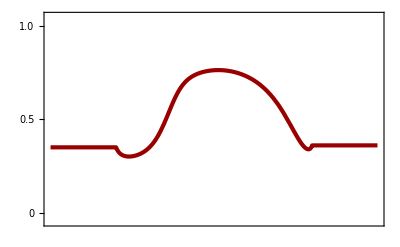
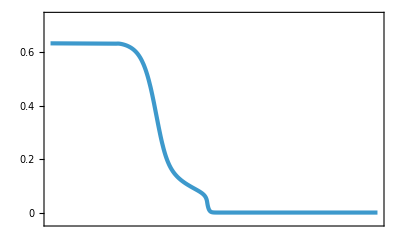
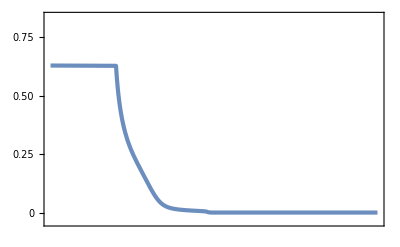
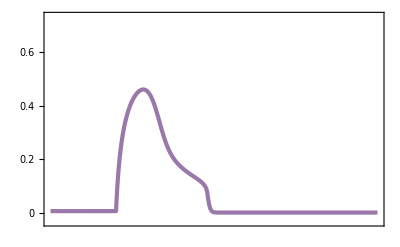
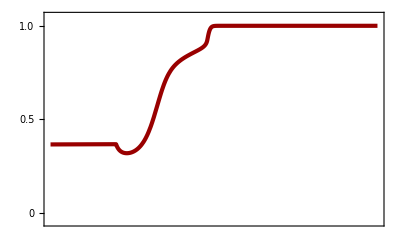

```mathematica
simulationPlotsHill=Table[Table[plotSimulation[x,Join[{w->temp},dailyPars],{2 3600,22 3600},{PlotStyle->{{thickness,x/.colors}},FrameLabel->{{x/.units,None},{None,None}},FrameTicks->{autoTicks,{dayTicks,None}},Evaluate@imageSizePadding[ImagePaddingLeftUnit1],PlotRange->{{2 3600,22 3600},{(-0.05(x/.maxRangesHillSimulations))+1.05(x/.minRangesHillSimulations),1.05x/.maxRangesHillSimulations}}}],{x,{FvFm,YP,YN,YU}}],{temp,dailyTemps}]
```

```mathematica
modTempLabels=Style[Row[{"Moderate temperature ",#,w/.units," "widgetModerate(*Rasterize[Magnify[widgetModerate,.1]]*)}],12,FontFamily->font]&/@{temperaturesHill[[1]], dailyTemps[[1]]}
heatTempLabels=Style[Row[{"Heat stress  ",#,w/.units,"    ",widgetHeat(*Rasterize[Magnify[widgetHeat,.7]]*)}],12,FontFamily->font]&/@{temperaturesHill[[2]], dailyTemps[[2]]}
```

{Moderate temperature 25°C  -Graphics-,Moderate temperature 25°C  -Graphics-}

{Heat stress  31°C    -Graphics-,Heat stress  31°C    -Graphics-}

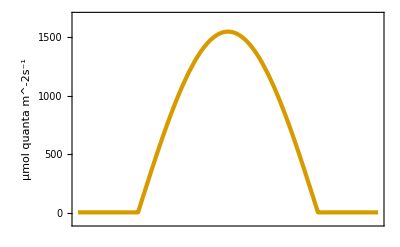
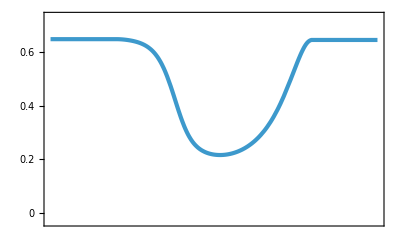
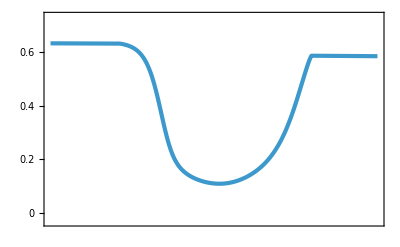
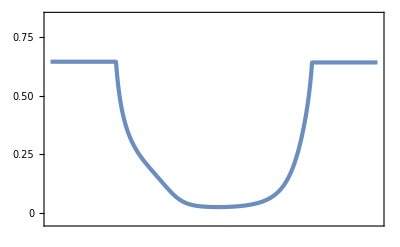
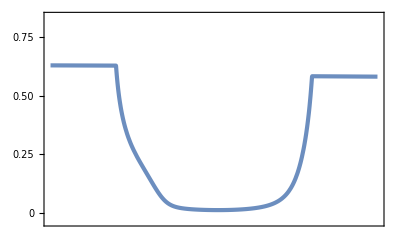
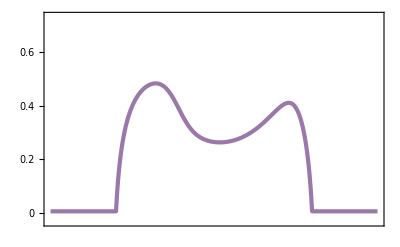
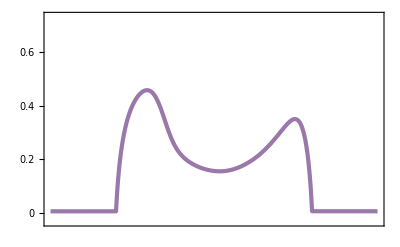
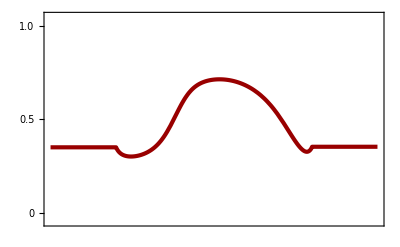
Data |  | Simulation | 
Light |  |  | 
-Graphics- |  | -Graphics- | 
Moderate temperature 25°C  -Graphics- | Heat stress  31°C    -Graphics- | Moderate temperature 25°C  -Graphics- | Heat stress  31°C    -Graphics-
Photosynthetic efficiency F_V/F_M |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Proportion photochemistry |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Proportion NPQ |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-
Proportion other loss |  |  | 
-Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
(Export[NotebookDirectory[]<>"export/simulation-data-daily.pdf",#];#)&@Style[(*Framed[*)Grid[
{
{"Data",SpanFromLeft,"Simulation",SpanFromLeft},
{"Light",SpanFromLeft},
{dataPlotHillLight,SpanFromLeft,simulationPlotsHillLight,SpanFromLeft},
{modTempLabels[[1]],heatTempLabels[[1]],modTempLabels[[2]],heatTempLabels[[2]]},(*
{"Temperature",SpanFromLeft},
{experimentPlotHillTemperature[[1]],experimentPlotHillTemperature[[2]],simulationPlotsHillTemperature[[1]],simulationPlotsHillTemperature[[2]]},*)
{"Photosynthetic efficiency F_V/F_M",SpanFromLeft},
{dataPlotsHill[[1,1]],dataPlotsHill[[2,1]],simulationPlotsHill[[1,1]],simulationPlotsHill[[2,1]]},
{"Proportion photochemistry",SpanFromLeft},
{dataPlotsHill[[1,2]],dataPlotsHill[[2,2]],simulationPlotsHill[[1,2]],simulationPlotsHill[[2,2]]},
{"Proportion NPQ",SpanFromLeft},
{dataPlotsHill[[1,3]],dataPlotsHill[[2,3]],simulationPlotsHill[[1,3]],simulationPlotsHill[[2,3]]},
{"Proportion other loss",SpanFromLeft},
{dataPlotsHill[[1,4]],dataPlotsHill[[2,4]],simulationPlotsHill[[1,4]],simulationPlotsHill[[2,4]]}
},
Spacings->{{1,5->1},1.1},
Dividers->{Flatten@{False,Table[True,{3}],False},Flatten@{False,True,False,True,True,Table[{False,True},{4}],False}}
](*,
RoundingRadius->10
]*),
FontFamily->font,14,LineBreakWithin->False
]
```

```mathematica
Table[Export[NotebookDirectory[]<>"export/"<>figureDirectoryDaily<>"/"<>figureNameDaily<>"-temperature="<>ToString[temperature]<>".pdf",#]&@fullSimulationPanel[Join[{w->temperature},dailyPars],{2 3600,22 3600},{FrameTicks->{autoTicks,{dayTicks,None}}},{(FrameLabel->{{#/.units,None},{None,None}})}&], {temperature,dailyTemps}];
```